# Battle of Coronel

## Introduction

In this notebook we calibrate the Heterogeneous Salvo Combat Model (HSCM), [MJ1, AAp1], to the First World War Battle of Coronel, [Wk1]. Our goal is to exemplify the usage of the functionalities of the paclet "SalvoCombatModeling", [AAp1]. We closely follow the Section B of Chapter III of [MJ1]. The calibration data used in [MJ1] is taken from [TB1].

## Setup

Here we load the paclet:

```mathematica
Needs["AntonAntonov`SalvoCombatModeling`"]
```

## The battle

The Battle of Coronel was a First World War Imperial German Navy victory over the Royal Navy on 1 November 1914, off the coast of central Chile near the city of Coronel.

The Battle of Coronel is a First World War naval engagement between three British ships {Good Hope, Monmouth, and Glasgow) and four German ships (Scharnhorst, Gneisenau, Leipzig, and Dresden).  The battle happened on 1 November 1914, off the coast of central Chile near the city of Coronel.

The Scharnhorst and Gneisenau are the first ships to open fire at Good Hope and Monmouth; the three British ships soon afterwards return fire. Dresden and Leipzig open fire on Glasgow, driving her out of the engagement. At the end of the battle, both Good Hope and Monmouth are sunk, while Glasgow, Scharnhorst, and Gneisenau were damaged.

```mathematica
Dataset[Transpose[{{"Good Hope", "Monmouth","Glasgow","Scharnhorst", "Gneisenau", "Leipzig",  "Dresden"},
{0,0,15,28,28,2,2}}]][All,AssociationThread[{"Ship","Duration of fire"},#]&]
```

The following graph shows which ship shot at which ships and total fire duration (in minutes):

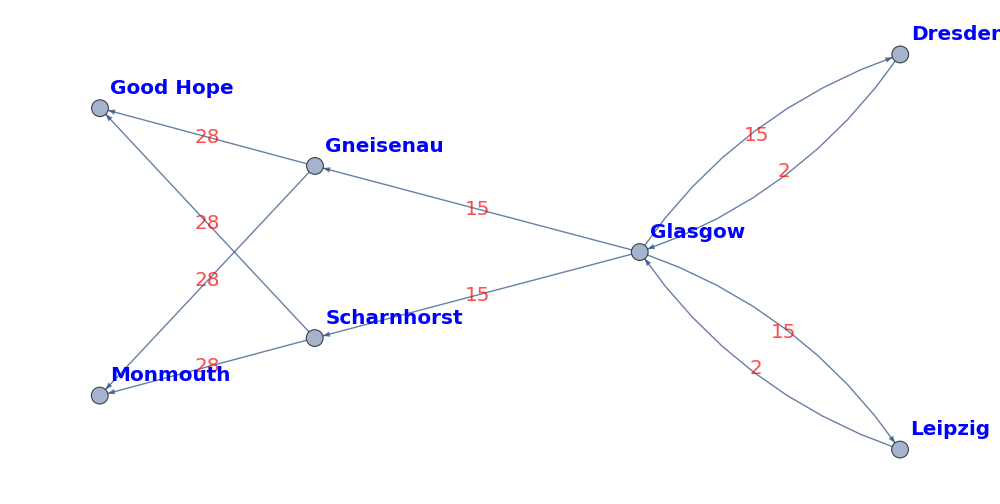

```mathematica
Graph[{
DirectedEdge["Scharnhorst","Good Hope",28],
DirectedEdge["Scharnhorst","Monmouth",28],
DirectedEdge["Gneisenau","Good Hope",28],
DirectedEdge["Gneisenau","Monmouth",28],
DirectedEdge["Leipzig","Glasgow",2],
DirectedEdge["Dresden","Glasgow",2],
DirectedEdge["Glasgow","Scharnhorst",15],
DirectedEdge["Glasgow","Gneisenau",15],
DirectedEdge["Glasgow","Leipzig",15],
DirectedEdge["Glasgow","Dresden",15]
},
VertexLabels->"Name",
VertexLabelStyle->Directive[Blue,Bold,20],
EdgeLabels->"EdgeTag",
EdgeLabelStyle->Directive[Red,Italic,20,Background->Yellow],
ImageSize->1000]
```

## Model

The British ships are in Good Hope, Monmouth, and Glasgow. They correspond to the indices 1, ,2, and 3 respectively.

```mathematica
AssociationThread[Range[3],{"Good Hope", "Monmouth","Glasgow"}]
```

<|1→Good Hope,2→Monmouth,3→Glasgow|>

The German ships are Scharnhorst, Gneisenau, Leipzig, and Dresden:

```mathematica
AssociationThread[Range[4],{"Scharnhorst", "Gneisenau", "Leipzig",  "Dresden"}]
```

<|1→Scharnhorst,2→Gneisenau,3→Leipzig,4→Dresden|>

Remark: The Battle of Coronel is modeled with a "typical" salvo model -- the ships use "continuous fire." Hence, there are no interceptors and or, in model terms, defense terms or matrices.

Here is the model (for 3 British ships and 4 German ships):

```mathematica
m=HeterogeneousSalvoModel[{B,3},{G,4},"OffensiveEffectivenessTerms"->True]
```

<|B→<|Units→{B[1],B[2],B[3]},OffenseMatrix→{{(β[G,B,1,1] Ψ[G,B,1,1] ε[G,B,1,1])/ζ[B,1],(β[G,B,2,1] Ψ[G,B,2,1] ε[G,B,2,1])/ζ[B,1],(β[G,B,3,1] Ψ[G,B,3,1] ε[G,B,3,1])/ζ[B,1],(β[G,B,4,1] Ψ[G,B,4,1] ε[G,B,4,1])/ζ[B,1]},{(β[G,B,1,2] Ψ[G,B,1,2] ε[G,B,1,2])/ζ[B,2],(β[G,B,2,2] Ψ[G,B,2,2] ε[G,B,2,2])/ζ[B,2],(β[G,B,3,2] Ψ[G,B,3,2] ε[G,B,3,2])/ζ[B,2],(β[G,B,4,2] Ψ[G,B,4,2] ε[G,B,4,2])/ζ[B,2]},{(β[G,B,1,3] Ψ[G,B,1,3] ε[G,B,1,3])/ζ[B,3],(β[G,B,2,3] Ψ[G,B,2,3] ε[G,B,2,3])/ζ[B,3],(β[G,B,3,3] Ψ[G,B,3,3] ε[G,B,3,3])/ζ[B,3],(β[G,B,4,3] Ψ[G,B,4,3] ε[G,B,4,3])/ζ[B,3]}},DefenseMatrix→{{(γ[B,G,1,1] δ[B,G,1,1] Θ[B,G,1,1] τ[B,G,1,1])/ζ[B,1]+(γ[B,G,1,2] δ[B,G,1,2] Θ[B,G,1,2] τ[B,G,1,2])/ζ[B,1]+(γ[B,G,1,3] δ[B,G,1,3] Θ[B,G,1,3] τ[B,G,1,3])/ζ[B,1]+(γ[B,G,1,4] δ[B,G,1,4] Θ[B,G,1,4] τ[B,G,1,4])/ζ[B,1],0,0},{0,(γ[B,G,2,1] δ[B,G,2,1] Θ[B,G,2,1] τ[B,G,2,1])/ζ[B,2]+(γ[B,G,2,2] δ[B,G,2,2] Θ[B,G,2,2] τ[B,G,2,2])/ζ[B,2]+(γ[B,G,2,3] δ[B,G,2,3] Θ[B,G,2,3] τ[B,G,2,3])/ζ[B,2]+(γ[B,G,2,4] δ[B,G,2,4] Θ[B,G,2,4] τ[B,G,2,4])/ζ[B,2],0},{0,0,(γ[B,G,3,1] δ[B,G,3,1] Θ[B,G,3,1] τ[B,G,3,1])/ζ[B,3]+(γ[B,G,3,2] δ[B,G,3,2] Θ[B,G,3,2] τ[B,G,3,2])/ζ[B,3]+(γ[B,G,3,3] δ[B,G,3,3] Θ[B,G,3,3] τ[B,G,3,3])/ζ[B,3]+(γ[B,G,3,4] δ[B,G,3,4] Θ[B,G,3,4] τ[B,G,3,4])/ζ[B,3]}}|>,G→<|Units→{G[1],G[2],G[3],G[4]},OffenseMatrix→{{(β[B,G,1,1] Ψ[B,G,1,1] ε[B,G,1,1])/ζ[G,1],(β[B,G,2,1] Ψ[B,G,2,1] ε[B,G,2,1])/ζ[G,1],(β[B,G,3,1] Ψ[B,G,3,1] ε[B,G,3,1])/ζ[G,1]},{(β[B,G,1,2] Ψ[B,G,1,2] ε[B,G,1,2])/ζ[G,2],(β[B,G,2,2] Ψ[B,G,2,2] ε[B,G,2,2])/ζ[G,2],(β[B,G,3,2] Ψ[B,G,3,2] ε[B,G,3,2])/ζ[G,2]},{(β[B,G,1,3] Ψ[B,G,1,3] ε[B,G,1,3])/ζ[G,3],(β[B,G,2,3] Ψ[B,G,2,3] ε[B,G,2,3])/ζ[G,3],(β[B,G,3,3] Ψ[B,G,3,3] ε[B,G,3,3])/ζ[G,3]},{(β[B,G,1,4] Ψ[B,G,1,4] ε[B,G,1,4])/ζ[G,4],(β[B,G,2,4] Ψ[B,G,2,4] ε[B,G,2,4])/ζ[G,4],(β[B,G,3,4] Ψ[B,G,3,4] ε[B,G,3,4])/ζ[G,4]}},DefenseMatrix→{{(γ[G,B,1,1] δ[G,B,1,1] Θ[G,B,1,1] τ[G,B,1,1])/ζ[G,1]+(γ[G,B,1,2] δ[G,B,1,2] Θ[G,B,1,2] τ[G,B,1,2])/ζ[G,1]+(γ[G,B,1,3] δ[G,B,1,3] Θ[G,B,1,3] τ[G,B,1,3])/ζ[G,1],0,0,0},{0,(γ[G,B,2,1] δ[G,B,2,1] Θ[G,B,2,1] τ[G,B,2,1])/ζ[G,2]+(γ[G,B,2,2] δ[G,B,2,2] Θ[G,B,2,2] τ[G,B,2,2])/ζ[G,2]+(γ[G,B,2,3] δ[G,B,2,3] Θ[G,B,2,3] τ[G,B,2,3])/ζ[G,2],0,0},{0,0,(γ[G,B,3,1] δ[G,B,3,1] Θ[G,B,3,1] τ[G,B,3,1])/ζ[G,3]+(γ[G,B,3,2] δ[G,B,3,2] Θ[G,B,3,2] τ[G,B,3,2])/ζ[G,3]+(γ[G,B,3,3] δ[G,B,3,3] Θ[G,B,3,3] τ[G,B,3,3])/ζ[G,3],0},{0,0,0,(γ[G,B,4,1] δ[G,B,4,1] Θ[G,B,4,1] τ[G,B,4,1])/ζ[G,4]+(γ[G,B,4,2] δ[G,B,4,2] Θ[G,B,4,2] τ[G,B,4,2])/ζ[G,4]+(γ[G,B,4,3] δ[G,B,4,3] Θ[G,B,4,3] τ[G,B,4,3])/ζ[G,4]}}|>|>

Remove the defense matrices:

```mathematica
m=Cancel[m//.γ[___]->0]
```

<|B→<|Units→{B[1],B[2],B[3]},OffenseMatrix→{{(β[G,B,1,1] ε[G,B,1,1] Ψ[G,B,1,1])/ζ[B,1],(β[G,B,2,1] ε[G,B,2,1] Ψ[G,B,2,1])/ζ[B,1],(β[G,B,3,1] ε[G,B,3,1] Ψ[G,B,3,1])/ζ[B,1],(β[G,B,4,1] ε[G,B,4,1] Ψ[G,B,4,1])/ζ[B,1]},{(β[G,B,1,2] ε[G,B,1,2] Ψ[G,B,1,2])/ζ[B,2],(β[G,B,2,2] ε[G,B,2,2] Ψ[G,B,2,2])/ζ[B,2],(β[G,B,3,2] ε[G,B,3,2] Ψ[G,B,3,2])/ζ[B,2],(β[G,B,4,2] ε[G,B,4,2] Ψ[G,B,4,2])/ζ[B,2]},{(β[G,B,1,3] ε[G,B,1,3] Ψ[G,B,1,3])/ζ[B,3],(β[G,B,2,3] ε[G,B,2,3] Ψ[G,B,2,3])/ζ[B,3],(β[G,B,3,3] ε[G,B,3,3] Ψ[G,B,3,3])/ζ[B,3],(β[G,B,4,3] ε[G,B,4,3] Ψ[G,B,4,3])/ζ[B,3]}},DefenseMatrix→{{0,0,0},{0,0,0},{0,0,0}}|>,G→<|Units→{G[1],G[2],G[3],G[4]},OffenseMatrix→{{(β[B,G,1,1] ε[B,G,1,1] Ψ[B,G,1,1])/ζ[G,1],(β[B,G,2,1] ε[B,G,2,1] Ψ[B,G,2,1])/ζ[G,1],(β[B,G,3,1] ε[B,G,3,1] Ψ[B,G,3,1])/ζ[G,1]},{(β[B,G,1,2] ε[B,G,1,2] Ψ[B,G,1,2])/ζ[G,2],(β[B,G,2,2] ε[B,G,2,2] Ψ[B,G,2,2])/ζ[G,2],(β[B,G,3,2] ε[B,G,3,2] Ψ[B,G,3,2])/ζ[G,2]},{(β[B,G,1,3] ε[B,G,1,3] Ψ[B,G,1,3])/ζ[G,3],(β[B,G,2,3] ε[B,G,2,3] Ψ[B,G,2,3])/ζ[G,3],(β[B,G,3,3] ε[B,G,3,3] Ψ[B,G,3,3])/ζ[G,3]},{(β[B,G,1,4] ε[B,G,1,4] Ψ[B,G,1,4])/ζ[G,4],(β[B,G,2,4] ε[B,G,2,4] Ψ[B,G,2,4])/ζ[G,4],(β[B,G,3,4] ε[B,G,3,4] Ψ[B,G,3,4])/ζ[G,4]}},DefenseMatrix→{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}|>|>

Put tooltip interpretations of the terms:

```mathematica
Block[{vrules=Map[#[[1]]->Tooltip[#[[1]],#[[2]],]&,SalvoVariableRules[{B,3},{G,4}]]},
ReplaceAll[m,vrules]
]
```

<|B→<|Units→{B[1],B[2],B[3]},OffenseMatrix→{{(β[G,B,1,1] ε[G,B,1,1] Ψ[G,B,1,1])/ζ[B,1],(β[G,B,2,1] ε[G,B,2,1] Ψ[G,B,2,1])/ζ[B,1],(β[G,B,3,1] ε[G,B,3,1] Ψ[G,B,3,1])/ζ[B,1],(β[G,B,4,1] ε[G,B,4,1] Ψ[G,B,4,1])/ζ[B,1]},{(β[G,B,1,2] ε[G,B,1,2] Ψ[G,B,1,2])/ζ[B,2],(β[G,B,2,2] ε[G,B,2,2] Ψ[G,B,2,2])/ζ[B,2],(β[G,B,3,2] ε[G,B,3,2] Ψ[G,B,3,2])/ζ[B,2],(β[G,B,4,2] ε[G,B,4,2] Ψ[G,B,4,2])/ζ[B,2]},{(β[G,B,1,3] ε[G,B,1,3] Ψ[G,B,1,3])/ζ[B,3],(β[G,B,2,3] ε[G,B,2,3] Ψ[G,B,2,3])/ζ[B,3],(β[G,B,3,3] ε[G,B,3,3] Ψ[G,B,3,3])/ζ[B,3],(β[G,B,4,3] ε[G,B,4,3] Ψ[G,B,4,3])/ζ[B,3]}},DefenseMatrix→{{0,0,0},{0,0,0},{0,0,0}}|>,G→<|Units→{G[1],G[2],G[3],G[4]},OffenseMatrix→{{(β[B,G,1,1] ε[B,G,1,1] Ψ[B,G,1,1])/ζ[G,1],(β[B,G,2,1] ε[B,G,2,1] Ψ[B,G,2,1])/ζ[G,1],(β[B,G,3,1] ε[B,G,3,1] Ψ[B,G,3,1])/ζ[G,1]},{(β[B,G,1,2] ε[B,G,1,2] Ψ[B,G,1,2])/ζ[G,2],(β[B,G,2,2] ε[B,G,2,2] Ψ[B,G,2,2])/ζ[G,2],(β[B,G,3,2] ε[B,G,3,2] Ψ[B,G,3,2])/ζ[G,2]},{(β[B,G,1,3] ε[B,G,1,3] Ψ[B,G,1,3])/ζ[G,3],(β[B,G,2,3] ε[B,G,2,3] Ψ[B,G,2,3])/ζ[G,3],(β[B,G,3,3] ε[B,G,3,3] Ψ[B,G,3,3])/ζ[G,3]},{(β[B,G,1,4] ε[B,G,1,4] Ψ[B,G,1,4])/ζ[G,4],(β[B,G,2,4] ε[B,G,2,4] Ψ[B,G,2,4])/ζ[G,4],(β[B,G,3,4] ε[B,G,3,4] Ψ[B,G,3,4])/ζ[G,4]}},DefenseMatrix→{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}|>|>

### Concrete parameter values

Setting the parameter values as in [MJ1]:

```mathematica
ClearAll[β,ζ,ε,Ψ]
```

```mathematica
β[G,B,1,1]=2.16;
β[G,B,1,2]=2.16;
β[G,B,1,3]=2.16;

β[G,B,2,1]=2.16;
β[G,B,2,2]=2.16;
β[G,B,2,3]=2.16;

β[G,B,3,1]=2.165;
β[G,B,3,2]=2.165;
β[G,B,3,3]=2.165;

β[G,B,4,1]=2.165;
β[G,B,4,2]=2.165;
β[G,B,4,3]=2.165;
```

```mathematica
ζ[B,1]=1.605;
ζ[B,2]=1.605;
ζ[B,3]=1.23;
```

```mathematica
ε[G,B,1,1]=0.028;
ε[G,B,1,2]=0.028;
ε[G,B,1,3]=0.028;
ε[G,B,2,1]=0.028;
ε[G,B,2,2]=0.028;
ε[G,B,2,3]=0.028;

ε[G,B,3,1]=0.012;
ε[G,B,3,2]=0.012;
ε[G,B,3,3]=0.012;
ε[G,B,4,1]=0.012;
ε[G,B,4,2]=0.012;
ε[G,B,4,3]=0.012;
```

```mathematica
Ψ[G,B,1,1]=0.5;
Ψ[G,B,1,2]=0.5;
Ψ[G,B,2,1]=0.5;
Ψ[G,B,2,2]=0.5;

Ψ[G,B,3,1]=0;
Ψ[G,B,3,2]=0;
Ψ[G,B,4,1]=0;
Ψ[G,B,4,2]=0;

Ψ[G,B,1,3]=0;
Ψ[G,B,2,3]=0;
Ψ[G,B,3,3]=1;
Ψ[G,B,4,3]=1;
```

### Damage calculations

```mathematica
m["B"]["OffenseMatrix"]
```

{{0.0188411,0.0188411,0.,0.},{0.0188411,0.0188411,0.,0.},{0.,0.,0.021122,0.021122}}

```mathematica
ΔB=Total/@m["B"]["OffenseMatrix"]
```

{0.0376822,0.0376822,0.0422439}

How many salvos to achieve total damage of Good Hope and Monmouth:

```mathematica
1/ΔB[[1]]
```

26.5377

That is close to the 28 min of fire by Scharnhorst and Gneisenau at Good Hope and Monmouth.

Total damage of on Glasgow -- Leipzig and Dresden fire for 2 min at Glasgow:

```mathematica
ΔB[[3]]*2
```

0.0844878

## References

### Articles, theses

[MJ1] Michael D. Johns, Steven E. Pilnick, Wayne P. Hughes, "Heterogeneous Salvo Model for the Navy After Next", (2000), Defense Technical Information Center.

[TB1] Thomas R. Beall, "The Development of a Naval Battle Model and Its Validation Using Historical Data", (1990),  Defense Technical Information Center.

[Wk1] Wikipedia entry, Salvo combat model.

### Paclets

[AAp1] Anton  Antonov, "SalvoCombatModeling", (2024), Wolfram Language Paclet Repository.

Related Guides

Heterogeneous Salvo Combat Modeling

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/SalvoCombatModeling

AntonAntonov`SalvoCombatModeling`

AntonAntonov/SalvoCombatModeling/tutorial/TheBattleofCoronel

### Keywords